## Orifice

```mathematica
domain="Pneumatic";
displayName="Orifice";
brief="Pneumatic orifice";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
Date[]
```

```mathematica
eps=.
```

```mathematica
inputParameters = {
{Cd,0.65,double,"","Discharge coefficient"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718,double,"J/Kg K","heatcoeff"},
{eps,0.02,double,"","Linearisation coeff"}
};
```

```mathematica
inputVariables = {
{A0,1.*10^-6,double,"m2","Area"}
};
```

```mathematica
portConnections = {
PneumaticQport[p1,100000.,"fluid port 1",{0,0.5,270}],
PneumaticQport[p2,100000.,"fluid port 2",{1,0.5,90}]
};
```

```mathematica
nodeConnections = {
PneumaticQnode[p1,100000.,"fluid port 1"],
PneumaticQnode[p2,100000.,"fluid port 2"]
};
```

qmp1 = qp1;
qmp2 = qp2;

### The system of equations

The flow at inlet and outlet are equal but with oposit sign.

```mathematica
qmp2=.
```

```mathematica
qmp1e = -qmp2;
```

```mathematica
Ng1=1
```

1

```mathematica
qma:=(pp1 Cd A0 Kg Ng)/(√Tp1)
```

```mathematica
qmb:=(pp2 Cd A0 Kg Ng)/(√Tp2)
```

```mathematica
Nga2:=keps (signedSquareL[((pp2/pp1)^(2/kappa)-(pp2/pp1)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ngb2:=keps(signedSquareL[((pp1/pp2)^(2/kappa)-(pp1/pp2)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ng:= onPositive[pp1-pp2](onPositive[pp2/pp1-crit]Nga2 + onNegative[pp2/pp1-crit]Ng1 )
	+ onNegative[pp1-pp2](onPositive[pp1/pp2-crit]Ngb2 + onNegative[pp1/pp2-crit]Ng1 );
```

```mathematica
dEp1q =(onPositive[qmp1e] qmp1e cv Tp2+onNegative[qmp1e]qmp1e  Tp1 cv);
dEp1ew = (onPositive[qmp1e] qmp1e R Tp2+onNegative[qmp1e]qmp1e Tp1  R);
dEp1gh=R onPositive[qmp1e] qmp1e Tp2 (1-pp1/pp2);
```

```mathematica
dEp2q =(onPositive[qmp2] qmp2 cv Tp1+onNegative[qmp2]qmp2  Tp2 cv);
dEp2ew = (onPositive[qmp2] qmp2 R Tp1+onNegative[qmp2]qmp2 Tp2  R);
dEp2gh=R onPositive[qmp2] qmp2 Tp1 (1-pp2/pp1);
```

### Plotting flow as a function of pressure

#### Parameters

```mathematica
Fa1[qmp2_,pp1_,pp2_]:=qmp2-( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb)
```

```mathematica
keps=1/(-√eps+√(1+eps));
		Kg=√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1)));
		Ndenom=(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1));
		crit=(2/(kappa+1))^(kappa/(kappa-1));
signedSquareL[x_,x0_]:=√(x+x0)-√x0
```

```mathematica
onPositive[x_]:=(1+Sign[x])/2;
onNegative[x_]:=1-(1+Sign[x])/2;
```

```mathematica
eps =0.1;
kappa = 1.4;
R = 287;
cv = 718;
Cd = 0.65;
A0 = 0.00001;
Tp1=200;
Tp2=200;
pp1 =10^5;
p10=pp1;
p20=pp2;
```

```mathematica
Fa1[qmp2,pp1,pp2]
```

qmp2+9.28855×10^-9 pp2 (1+1/2 (-1-Sign[100000-pp2])) (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))-0.000464427 (1+Sign[100000-pp2])^2 (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
AFa1[pp1_,pp2_]:= qmp2/.FindRoot[Fa1[qmp2,pp1,pp2]==0,{qmp2,2}]
```

```mathematica
pp2=.
```

```mathematica
crit
```

0.528282

```mathematica
Ng
```

1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
p10=pp1;
p20=pp2;
```

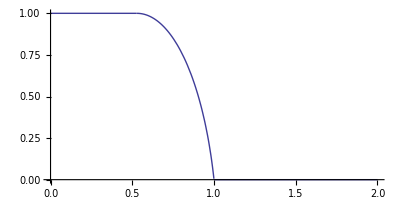

```mathematica
ParametricPlot[{pp2/pp1,Ng},{pp2,1,200000}]
```

```mathematica
qma
```

0.000928855 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
Tp1
```

200

```mathematica
qmp2 =.
```

```mathematica
nmax=100;
qmlist=Array[a1,nmax];
qmdlist=Array[a2,{nmax,2}];
```

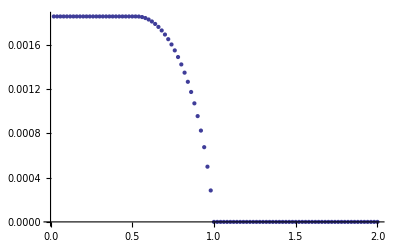

```mathematica
For[i=1,i<nmax+1,i++,
	pp2 = pp1 2 i/nmax;
	qmdlist[[i]]={pp2/pp1,AFa1[pp1,pp2]}
];
ListPlot[qmdlist]
```

```mathematica
eps =.;
kappa =.;
R = .;
cv = .;
Cd = .;
A0=.;
Tp1=.;
Tp2=.;
pp1=.;
pp2=.;
p10=.;
p20=.;
```

```mathematica
keps=.;
Kg=.;
Ndenom=.;
crit=.;
onPositive[x_]=.;
onNegative[x_]=.;
signedSquareL[x_,x0_]=.;
```

### Equations

Calculation of parameters

```mathematica
localExpressions ={
kappa==1+R/cv,
keps==1/(-√eps+√(1+eps)),
Kg==√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1))),
Ndenom==(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1)),
crit==(2/(kappa+1))^(kappa/(kappa-1)),
cp==cv+R
};
```

```mathematica
systemEquationsDA={
qmp2==( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb),
		dEp1==(onPositive[qmp1e] qmp1e cp Tp2+onNegative[qmp1e]qmp1e cp Tp1+R onPositive[qmp1e] qmp1e Tp2 (1-pp1/pp2)),
		dEp2==(onPositive[qmp2] qmp2 cp Tp1+onNegative[qmp2]qmp2 cp Tp2+R onPositive[qmp2] qmp2 Tp1 (1-pp2/pp1))		
	};
```

```mathematica
systemVariables = {qmp2,dEp1,dEp2,pp1,pp2};
```

### Boundarys

```mathematica
systemBoundaryEquations = { 
pp1 == (cp1 + Zcp1 dEp1 ),
pp2 ==(cp2 + Zcp2 dEp2 )
};
```

```mathematica
systemVariables
```

{qmp2,dEp1,dEp2,pp1,pp2}

### Expressions

The inlet flow is calculated as the outlet flow with reversed sign.

```mathematica
expressions = {
qmp1==-qmp2
};
```

Initial values

```mathematica
cp1/.Solve[systemBoundaryEquations,{cp1,cp2}][[1]]
```

pp1-dEp1 Zcp1

```mathematica
Compgen[file]
```